{Λc 1/2+ 2.287}

{2.26957,4.86221,{3.07849,2.95317,2.47977,2.04279}}

{0.603054}

{{0.18703},{0.177153}}

{Σc 1/2+ 2.454}

{2.41129,4.818,{3.07791,2.95157,2.47714,2.04279}}

{0.915314,0.597787,0.350856}

{{0.804105,0.15433,-0.495445},{0.761641,0.14618,-0.469281}}

{Σc^* 3/2+ 2.518}

{2.51166,5.00767,{3.0803,2.95822,2.48829,2.04279}}

{0.950734,0.620381,0.366263}

{{1.53851,0.525479,-0.487553},{1.45726,0.497728,-0.461806}}

{D 0- 1.867}

{1.83519,3.62953,{3.05738,2.89647,2.39954,2.04279}}

{0.456034,0.254338,0.254338,0.456034}

{D^* 1- 2.009}

{2.00872,4.08918,{3.06671,2.92104,2.43123,2.04279}}

{0.510909,0.291649,0.291649,0.510909}

{{0.457559,-0.369665,0.369665,-0.457559},{0.433396,-0.350143,0.350143,-0.433396}}

{Λb 1/2+ 5.620}

{5.64823,4.59725,{3.07489,2.94322,2.46376,2.04279}}

{0.254015}

{{-0.0323579},{-0.0306491}}

{Σb 1/2+ 5.813}

{5.83455,4.63682,{3.07545,2.94477,2.46619,2.04279}}

{0.714611,0.25627,0.615889}

{{0.844575,0.219235,-0.406106},{0.799974,0.207657,-0.384659}}

{Σb^* 3/2+ 5.833}

{5.87225,4.72773,{3.07671,2.94824,2.47172,2.04279}}

{0.728677,0.261451,0.627899}

{{1.24282,0.286423,-0.669977},{1.17719,0.271297,-0.634596}}

{B 0- 5.280}

{5.24831,3.1413,{3.04458,2.86402,2.36327,2.04279}}

{0.418344,0.17095,0.418344}

{B^* 1- 5.325}

{5.32522,3.47496,{3.05371,2.88701,2.38836,2.04279}}

{0.462412,0.190005,0.190005,0.462412}

{{0.500748,-0.202223,0.202223,-0.583749},{0.474304,-0.191544,0.191544,-0.552921}}

{Mass Spectrum}

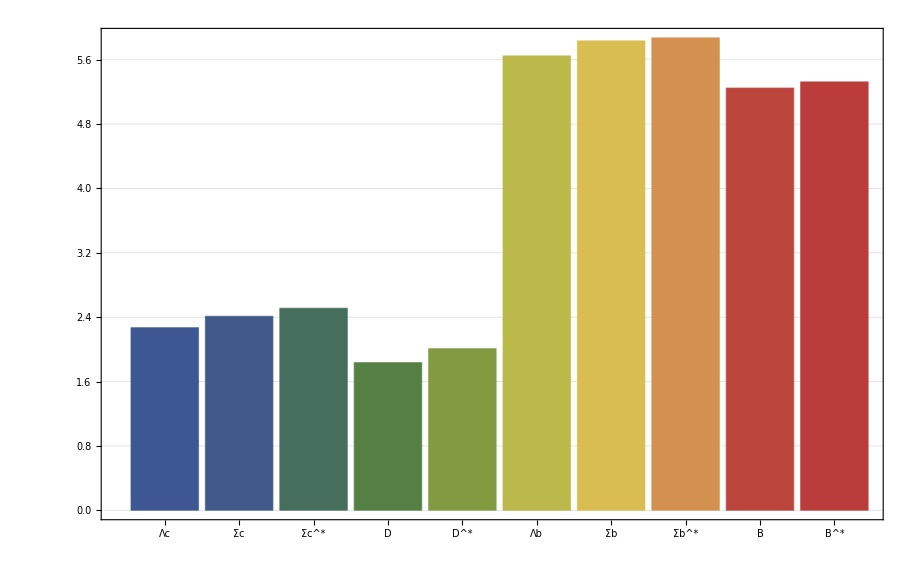

{My Error}

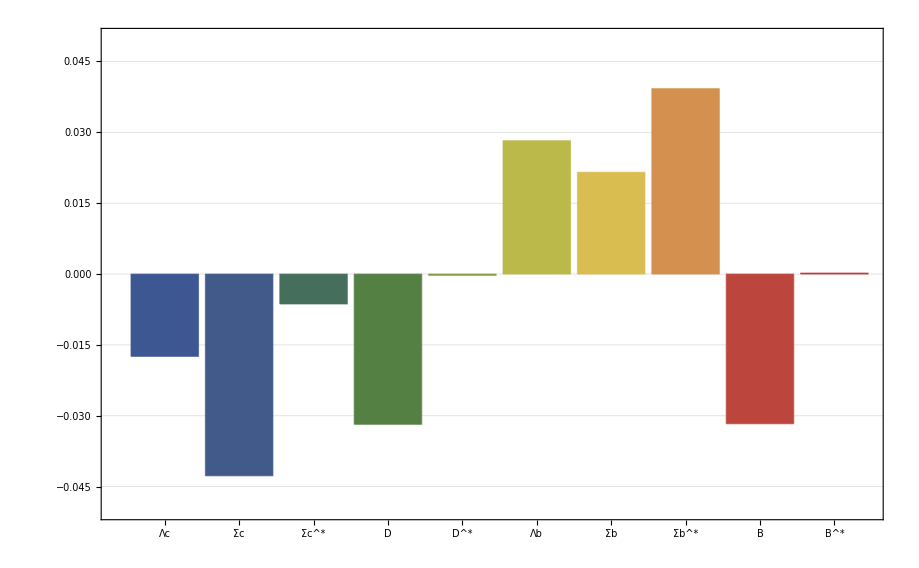

{Charge Radius}

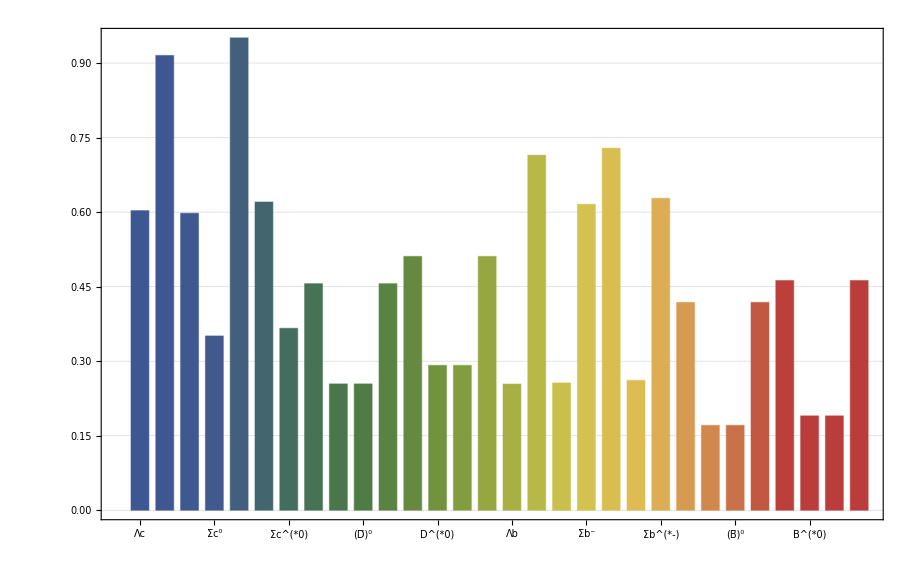

{Magnetic Moment}

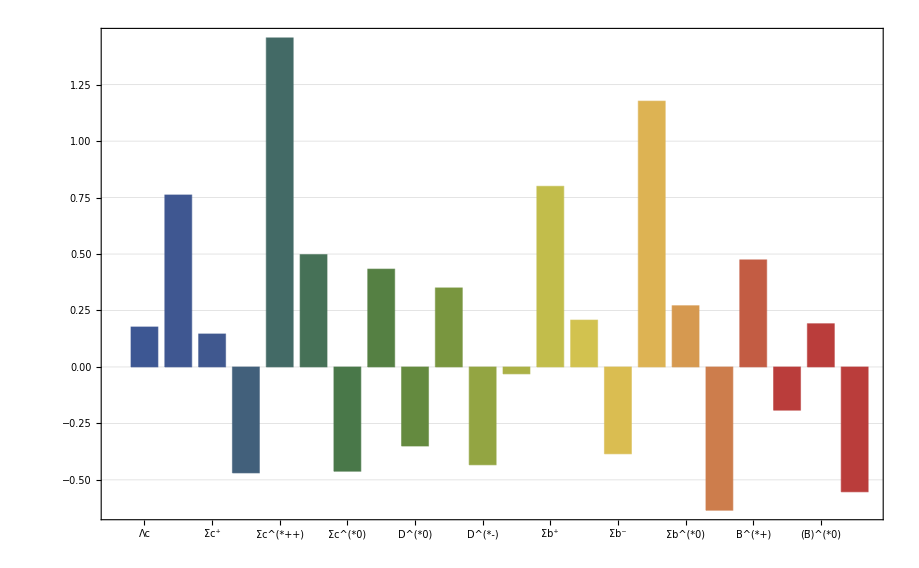

```mathematica
<<MITBagModel\MITBagModel.m

Nc=Hadron[{0,0,0,3},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,8}},0];
μNp=MagneticMoment[{0,0,0,4/3,-1/3},{0,0,0,0,0},Nc];

{"Λc 1/2+ 2.287"}
Λc=Hadron[{0,1,0,2},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,8}},0]
rΛc=ChargeRadius[{0,1,0,1,1},{0,0,0,0,0},Λc];
μΛc=MagneticMoment[{0,1,0,0,0},{0,0,0,0,0},Λc];
{rΛc}
{{μΛc},{μΛc/μNp}}

{"Σc 1/2+ 2.454"}
Σc=Hadron[{0,1,0,2},{{0,0,0,0},{0,0,0,32/3},{0,0,0,0},{0,0,0,-8/3}},0]
rΣcpp=ChargeRadius[{0,1,0,2,0},{0,0,0,0,0},Σc];
rΣcp=ChargeRadius[{0,1,0,1,1},{0,0,0,0,0},Σc];
rΣc0=ChargeRadius[{0,1,0,0,2},{0,0,0,0,0},Σc];
μΣcpp=MagneticMoment[{0,-1/3,0,4/3,0},{0,0,0,0,0},Σc];μΣcp=MagneticMoment[{0,-1/3,0,2/3,2/3},{0,0,0,0,0},Σc];μΣc0=MagneticMoment[{0,-1/3,0,0,4/3},{0,0,0,0,0},Σc];
{rΣcpp,rΣcp,rΣc0}
{{μΣcpp,μΣcp,μΣc0},{μΣcpp/μNp,μΣcp/μNp,μΣc0/μNp}}

{"Σc^* 3/2+ 2.518"}
SuperStar[Σc]=Hadron[{0,1,0,2},{{0,0,0,0},{0,0,0,-16/3},{0,0,0,0},{0,0,0,-8/3}},0]
SuperStar[rΣcpp]=ChargeRadius[{0,1,0,2,0},{0,0,0,0,0},SuperStar[Σc]];
SuperStar[rΣcp]=ChargeRadius[{0,1,0,1,1},{0,0,0,0,0},SuperStar[Σc]];
SuperStar[rΣc0]=ChargeRadius[{0,1,0,0,2},{0,0,0,0,0},SuperStar[Σc]];
SuperStar[μΣcpp]=MagneticMoment[{0,1,0,2,0},{0,0,0,0,0},SuperStar[Σc]];
SuperStar[μΣcp]=MagneticMoment[{0,1,0,1,1},{0,0,0,0,0},SuperStar[Σc]];
SuperStar[μΣc0]=MagneticMoment[{0,1,0,0,2},{0,0,0,0,0},SuperStar[Σc]];
{SuperStar[rΣcpp],SuperStar[rΣcp],SuperStar[rΣc0]}
{{SuperStar[μΣcpp],SuperStar[μΣcp],SuperStar[μΣc0]},{SuperStar[μΣcpp]/μNp,SuperStar[μΣcp]/μNp,SuperStar[μΣc0]/μNp}}

{"D 0- 1.867"}
Dq=Hadron[{0,1,0,1},{{0,0,0,0},{0,0,0,16},{0,0,0,0},{0,0,0,0}},0]
rDp=ChargeRadius[{0,1,0,0,0},{0,0,0,0,1},Dq];
rD0=ChargeRadius[{0,1,0,0,0},{0,0,0,1,0},Dq];
rD0bar=ChargeRadius[{0,0,0,1,0},{0,1,0,0,0},Dq];
rDm=ChargeRadius[{0,0,0,0,1},{0,1,0,0,0},Dq];
{rDp,rD0,rD0bar,rDm}

{"D^* 1- 2.009"}
SuperStar[Dq]=Hadron[{0,1,0,1},{{0,0,0,0},{0,0,0,-16/3},{0,0,0,0},{0,0,0,0}},0]
SuperStar[rDp]=ChargeRadius[{0,1,0,0,0},{0,0,0,0,1},SuperStar[Dq]];
SuperStar[rD0]=ChargeRadius[{0,1,0,0,0},{0,0,0,1,0},SuperStar[Dq]];
SuperStar[rD0bar]=ChargeRadius[{0,0,0,1,0},{0,1,0,0,0},SuperStar[Dq]];
SuperStar[rDm]=ChargeRadius[{0,0,0,0,1},{0,1,0,0,0},SuperStar[Dq]];
SuperStar[μDp]=MagneticMoment[{0,1,0,0,0},{0,0,0,0,1},SuperStar[Dq]];
SuperStar[μD0]=MagneticMoment[{0,1,0,0,0},{0,0,0,1,0},SuperStar[Dq]];
SuperStar[μD0bar]=MagneticMoment[{0,0,0,1,0},{0,1,0,0,0},SuperStar[Dq]];
SuperStar[μDm]=MagneticMoment[{0,0,0,0,1},{0,1,0,0,0},SuperStar[Dq]];
{SuperStar[rDp],SuperStar[rD0],SuperStar[rD0bar],SuperStar[rDm]}
{{SuperStar[μDp],SuperStar[μD0],SuperStar[μD0bar],SuperStar[μDm]},{SuperStar[μDp]/μNp,SuperStar[μD0]/μNp,SuperStar[μD0bar]/μNp,SuperStar[μDm]/μNp}}

{"Λb 1/2+ 5.620"}
Λb=Hadron[{1,0,0,2},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,8}},0]
rΛb=ChargeRadius[{1,0,0,1,1},{0,0,0,0,0},Λb];
μΛb=MagneticMoment[{1,0,0,0,0},{0,0,0,0,0},Λb];
{rΛb}
{{μΛb},{μΛb/μNp}}

{"Σb 1/2+ 5.813"}
Σb=Hadron[{1,0,0,2},{{0,0,0,32/3},{0,0,0,0},{0,0,0,0},{0,0,0,-8/3}},0]
rΣbp=ChargeRadius[{1,0,0,2,0},{0,0,0,0,0},Σb];
rΣb0=ChargeRadius[{1,0,0,1,1},{0,0,0,0,0},Σb];
rΣbm=ChargeRadius[{1,0,0,0,2},{0,0,0,0,0},Σb];
μΣbp=MagneticMoment[{-1/3,0,0,4/3,0},{0,0,0,0,0},Σb];μΣb0=MagneticMoment[{-1/3,0,0,2/3,2/3},{0,0,0,0,0},Σb];μΣbm=MagneticMoment[{-1/3,0,0,0,4/3},{0,0,0,0,0},Σb];
{rΣbp,rΣb0,rΣbm}
{{μΣbp,μΣb0,μΣbm},{μΣbp/μNp,μΣb0/μNp,μΣbm/μNp}}

{"Σb^* 3/2+ 5.833"}
SuperStar[Σb]=Hadron[{1,0,0,2},{{0,0,0,-16/3},{0,0,0,0},{0,0,0,0},{0,0,0,-8/3}},0]
SuperStar[rΣbp]=ChargeRadius[{1,0,0,2,0},{0,0,0,0,0},SuperStar[Σb]];
SuperStar[rΣb0]=ChargeRadius[{1,0,0,1,1},{0,0,0,0,0},SuperStar[Σb]];
SuperStar[rΣbm]=ChargeRadius[{1,0,0,0,2},{0,0,0,0,0},SuperStar[Σb]];
SuperStar[μΣbp]=MagneticMoment[{1,0,0,2,0},{0,0,0,0,0},SuperStar[Σb]];
SuperStar[μΣb0]=MagneticMoment[{1,0,0,1,1},{0,0,0,0,0},SuperStar[Σb]];
SuperStar[μΣbm]=MagneticMoment[{1,0,0,0,2},{0,0,0,0,0},SuperStar[Σb]];
{SuperStar[rΣbp],SuperStar[rΣb0],SuperStar[rΣbm]}
{{SuperStar[μΣbp],SuperStar[μΣb0],SuperStar[μΣbm]},{SuperStar[μΣbp]/μNp,SuperStar[μΣb0]/μNp,SuperStar[μΣbm]/μNp}}

{"B 0- 5.280"}
Bq=Hadron[{1,0,0,1},{{0,0,0,16},{0,0,0,0},{0,0,0,0},{0,0,0,0}},0]
rBp=ChargeRadius[{0,0,0,1,0},{1,0,0,0,0},Bq];
rB0=ChargeRadius[{0,0,0,0,1},{1,0,0,0,0},Bq];
rB0bar=ChargeRadius[{1,0,0,0,0},{0,0,0,0,1},Bq];
rBm=ChargeRadius[{1,0,0,0,0},{0,0,0,1,0},Bq];
{rBp,rB0,rBm}

{"B^* 1- 5.325"}
SuperStar[Bq]=Hadron[{1,0,0,1},{{0,0,0,-16/3},{0,0,0,0},{0,0,0,0},{0,0,0,0}},0]
SuperStar[rBp]=ChargeRadius[{0,0,0,1,0},{1,0,0,0,0},SuperStar[Bq]];
SuperStar[rB0]=ChargeRadius[{0,0,0,0,1},{1,0,0,0,0},SuperStar[Bq]];
SuperStar[rB0bar]=ChargeRadius[{1,0,0,0,0},{0,0,0,0,1},SuperStar[Bq]];
SuperStar[rBm]=ChargeRadius[{1,0,0,0,0},{0,0,0,1,0},SuperStar[Bq]];
SuperStar[μBp]=MagneticMoment[{0,0,0,1,0},{1,0,0,0,0},SuperStar[Bq]];
SuperStar[μB0]=MagneticMoment[{0,0,0,0,1},{1,0,0,0,0},SuperStar[Bq]];
SuperStar[μB0bar]=MagneticMoment[{1,0,0,0,0},{0,0,0,0,1},SuperStar[Bq]];
SuperStar[μBm]=MagneticMoment[{1,0,0,0,0},{0,0,0,1,0},SuperStar[Dq]];
{SuperStar[rBp],SuperStar[rB0],SuperStar[rB0bar],SuperStar[rBm]}
{{SuperStar[μBp],SuperStar[μB0],SuperStar[μB0bar],SuperStar[μBm]},{SuperStar[μBp]/μNp,SuperStar[μB0]/μNp,SuperStar[μB0bar]/μNp,SuperStar[μBm]/μNp}}

{"Mass Spectrum"}
BarChart[{First[Λc],First[Σc],First[SuperStar[Σc]],First[Dq],First[SuperStar[Dq]],First[Λb],First[Σb],First[SuperStar[Σb]],First[Bq],First[SuperStar[Bq]]},Frame->True,ChartLabels->{"Λc","Σc","Σc^*","D","D^*","Λb","Σb","Σb^*","B","B^*"},ChartStyle->"DarkRainbow",GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed]]

{"My Error"}
BarChart[{
(First[Λc]-2.287),
(First[Σc]-2.454),
(First[SuperStar[Σc]]-2.518),
(First[Dq]-1.867),
(First[SuperStar[Dq]]-2.009),
(First[Λb]-5.620),
(First[Σb]-5.813),
(First[SuperStar[Σb]]-5.833),
(First[Bq]-5.280),
(First[SuperStar[Bq]]-5.325)},Frame->True,ChartLabels->{"Λc","Σc","Σc^*","D","D^*","Λb","Σb","Σb^*","B","B^*"},ChartStyle->"DarkRainbow",PlotRange->{-0.05,0.05},GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed]]

{"Charge Radius"}
BarChart[{rΛc,rΣcpp,rΣcp,rΣc0,SuperStar[rΣcpp],SuperStar[rΣcp],SuperStar[rΣc0],rDp,rD0,rD0bar,rDm,SuperStar[rDp],SuperStar[rD0],SuperStar[rD0bar],SuperStar[rDm],rΛb,rΣbp,rΣb0,rΣbm,SuperStar[rΣbp],SuperStar[rΣb0],SuperStar[rΣbm],rBp,rB0,rB0bar,rBm,SuperStar[rBp],SuperStar[rB0],SuperStar[rB0bar],SuperStar[rBm]},Frame->True,ChartLabels->{"Λc","Σc^(++)","Σc^+","Σc^0","Σc^(*++)","Σc^(*+)","Σc^(*0)","D^+","D^0","(D̄)^0","D^-","D^(*+)","D^(*0)","(D̄)^(*0)","D^(*-)","Λb","Σb^+","Σb^0","Σb^-","Σb^(*+)","Σb^(*0)","Σb^(*-)","B^+","B^0","(B̄)^0","B^-","B^(*+)","B^(*0)","(B̄)^(*0)","B^(*-)"},ChartStyle->"DarkRainbow",GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed]]

{"Magnetic Moment"}
BarChart[{μΛc/μNp,μΣcpp/μNp,μΣcp/μNp,μΣc0/μNp,SuperStar[μΣcpp]/μNp,SuperStar[μΣcp]/μNp,SuperStar[μΣc0]/μNp,SuperStar[μDp]/μNp,SuperStar[μD0]/μNp,SuperStar[μD0bar]/μNp,SuperStar[μDm]/μNp,μΛb/μNp,μΣbp/μNp,μΣb0/μNp,μΣbm/μNp,SuperStar[μΣbp]/μNp,SuperStar[μΣb0]/μNp,SuperStar[μΣbm]/μNp,SuperStar[μBp]/μNp,SuperStar[μB0]/μNp,SuperStar[μB0bar]/μNp,SuperStar[μBm]/μNp},Frame->True,ChartLabels->{"Λc","Σc^(++)","Σc^+","Σc^0","Σc^(*++)","Σc^(*+)","Σc^(*0)","D^(*+)","D^(*0)","(D̄)^(*0)","D^(*-)","Λb","Σb^+","Σb^0","Σb^-","Σb^(*+)","Σb^(*0)","Σb^(*-)","B^(*+)","B^(*0)","(B̄)^(*0)","B^(*-)"},ChartStyle->"DarkRainbow",GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed]]
```